# Lab_Work_1

# 1.1

```mathematica
1. Используя функцию Range создайте список {1,2,3,4}
```

```mathematica
(*Range[i] генерирует список от 1 до i*)
```

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
2. Создайте список из натуральных чисел от 1 до 100
```

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
3.Используя функции Range и Reverse,создайте список {4,3,2,1}
```

```mathematica
(*Reverse[i] меняет порядок элементов в i на обратный*)
```

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
4.Создайте список из натуральных чисел от 1 до 50 в обратном порядке
```

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
5.Используя функции Range,Reverse и Join, создайте список {1,2,3,4,4,3,2,1}
```

```mathematica
(*Join[list1, list2, ...] объединяет списки или другие выражения*)
```

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

```mathematica
6. Нарисовать график списка чисел,которые возрастают от 1 до 100,а затем убывают от 100
до 1
```

```mathematica
(*ListLinePlot[{y1,y2,...}]строит линию через точки {1,y1}, {2,y2},...*)
```

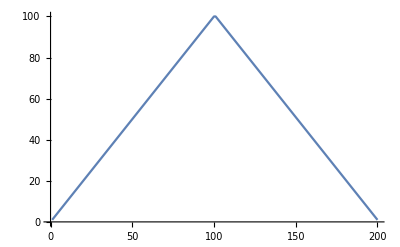

```mathematica
ListLinePlot[{Join[Range[100],Reverse[Range[100]]]}]
```

```mathematica
7. Используя функции Range и RandomInteger создайте список случайно генерированной
длины,не превышающей число 10
```

```mathematica
(*RandomInteger[{i}] генерирует псевдорандомное целое число от нуля до i *)
```

```mathematica
Range[RandomInteger[10]]
```

{1,2,3}

```mathematica
8.Найти простейшую форму для команды Reverse[Reverse[Range[10]]]
```

```mathematica
(*первый Reverse обратит порядок списка, но второй Reverse обратит его в первоначальный порядок, поэтому оба Reverse можно убрать*)
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]
```

```mathematica
(*Join сгруппирует сколько угодно списков и элементов и нету необходимости использовать второй Join внутри первого*)
```

```mathematica
Join[{1,2},{3,4},{5}]
```

{1,2,3,4,5}

```mathematica
10.Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]
```

```mathematica
(*Join сгруппирует сколько угодно списков и элементов и нету необходимости использовать второй Join внутри первого*)
```

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
11.Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]
```

```mathematica
(*Объединяются числа от 1 до 20 и от 20 до 1. При изменении порядка следования элементов списка на обратный, список не изменится*)
```

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

# 1.2 Strings and Text

```mathematica
1. Присоедините две копии строки «Здравствуйте».
```

```mathematica
(*StringRepeat["str", n] создаёт строку состоящую из "str", повторённого n раз*)
```

```mathematica
StringRepeat["Здравствуйте",2]
```

ЗдравствуйтеЗдравствуйте

```mathematica
2.Создайте единую строку всего английского алфавита заглавными буквами.
```

```mathematica
(*StringJoin соединяет строки*)
(*Alphabet[] выдаёт английский алфавит в виде списка из строчных букв
ToUpperCase представляет все символы в строке заглавными буквами*)
```

```mathematica
StringJoin[ToUpperCase[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
3.Сгенерируйте строку английского алфавита в обратном порядке.
```

```mathematica
StringJoin[Reverse[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
4. Объедините 100 копий строки «ABCD»
```

```mathematica
StringRepeat["ABCD",100]
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

```mathematica
5.Используйте StringTake,StringJoin и Alphabet,чтобы получить «abcdef».
```

```mathematica
(*StringTake["str",n] выдаёт строку, содержащую первые n символов из строки "str"*)
```

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
6. Создайте столбец с числом элементов,равных длине строки «это о строках» и содержащих
число букв (включая пробелы) равное номеру элемента.
```

```mathematica
(*Column [{e1, e2,...}] это столбец из элементов e1, e2 и так далее, при том, что e1 наверху
StringLength["str"] выдаёт длину строки "str"
Table[e, {i,n}] создаёт список значений e, где i зменяется от 1 до n*)
```

```mathematica
Column[Table [StringTake["это о строках", i],{i,StringLength["это о строках"]}]]
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

```mathematica
7. Создайте гистограмму длин слов в «Давным-давно,в далекой галактике,далеко».
```

```mathematica
(*BarChart[{y1, y2,...}] создаёт гистограмму со столбцами высотой y1, y2,...
TextWords выдаёт список слов из которых состоит заданная строка*)
```

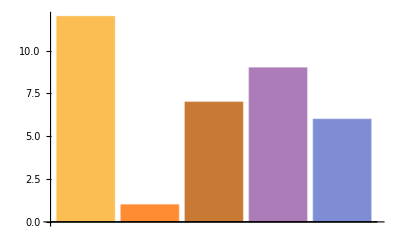

```mathematica
BarChart[{StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]}]
```

```mathematica
8. Найдите максимальную длину слова среди английских слов из WordList[]
```

```mathematica
(*Max[x1, x2,...] выдаёт самое большое число из предложенных
WordList[] выдаёт список распространённых слов
но без интернета он не работает, поэтому используем искусственных список*)
```

```mathematica
Max[StringLength[{"a","aah","aardvark","aback","abacus","abaft","abalone","abandon","abandoned","abandonment","abase","abasement","abash","zoo","zoological","zoologist","zoology","zoom","zoophyte","zounds","zucchini","zwieback","zydeco","zygote","zygotic","zymurgy"}]]
```

11

```mathematica
9. Используйте Length,чтобы найти длину русского алфавита.
```

```mathematica
(*Length[e] выдаёт число элементов в e*)
```

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.
```

```mathematica
StringJoin[Reverse[ToUpperCase[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

# 1.3

```mathematica
1. Используйте Range и чистую функцию для создания списка из квадратов первых 20
натуральных чисел.
```

```mathematica
(*x^n или Power[x, n] возводит x в степень n*)
```

```mathematica
#^2 &/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
2. Составьте список из результатов смешивания желтого,зеленого и синего цветов с красным
цветом.
```

```mathematica
(*Blend[{c1,c2},x] создаёт цвет, полученный при смешении 1-x цвета с1 и цвета с2*)
```

```mathematica
Blend[{#, Red},0.5] &/@{Yellow, Green, Blue}
```

{RGBColor[1., 0.5, 0.],RGBColor[0.5, 0.5, 0.],RGBColor[0.5, 0., 0.5]}

```mathematica
3. Создайте список столбцов в рамках,содержащих прописные и строчные версии каждой
буквы алфавита.
```

```mathematica
(*Framed создаёт рамку*)
```

```mathematica
Framed[Column[{ToUpperCase[#], #}]] &/@Alphabet["Russian"]
```

{А
а,Б
б,В
в,Г
г,Д
д,Е
е,Ё
ё,Ж
ж,З
з,И
и,Й
й,К
к,Л
л,М
м,Н
н,О
о,П
п,Р
р,С
с,Т
т,У
у,Ф
ф,Х
х,Ц
ц,Ч
ч,Ш
ш,Щ
щ,Ъ
ъ,Ы
ы,Ь
ь,Э
э,Ю
ю,Я
я}

```mathematica
4. Составьте список букв алфавита в случайных цветах в рамках,имеющих случайные цвета
фона
```

```mathematica
(*Hue[h] - графическая директива, которая указывает, что следующие объекты должны отображаться в цвете, соответствующем оттенку h
RandomReal[] выдаёт псевдослучайное число с плавающей точкой от 0 до 1*)
```

```mathematica
Framed[Style[#,Hue[RandomReal[]]], Background->Hue[RandomReal[]]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
5. Напишите в более простой форме команду (#^2+1&)/@Range[10].
```

```mathematica
(*Palettes->other->Basic Math Input в меню наверху или комбинация клавиш ctrl+6 создаёт ячейку для степени числа или переменной*)
```

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

# 1.4

```mathematica
1. Составьте список результатов использования функции Blur до 10 раз,начиная с
растрированного размера 30 “X” (Используйте:Rasterize[Style]).
```

```mathematica
(* Blur[image] выдаёт размытую версию изображения image
Rasterize[g] возвращает растрированное изображение g
NestList[f,x,n] выдаёт список результатов последовательного применения к x функции f в количестве от 0 до n*)
```

```mathematica
NestList[Blur, Rasterize[X,RasterSize->30], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
2. Начните с x,затем создайте список,использовав последовательно функцию Framed до 10
раз,используя каждый раз случайный цвет фона.
```

```mathematica
NestList[Framed[#,Background->Hue[RandomReal[]]]&, x, 10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
3. Начните с размера 50 для “A”,затем создайте список вложенного применения Framed и случайного вращения 5 раз.
```

```mathematica
(*Rotate[Obj, x Degree] - поворачивает объект Obj против часовой стрелки на x градусов относительно центра, ограничивающей объект рамки
Table[e, {i,n}] создаёт список значений e, где i зменяется от 1 до n
Rasterize[g] возвращает растрированное изображение g*)
```

```mathematica
Table[Rotate[Nest[Framed, Rasterize[A,RasterSize -> 50], i], RandomReal[{0,360}] Degree],{i,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-#)&,начиная с 0.2.
```

```mathematica
(*ListLinePlot[{y1,y2,...}]строит линию через точки {1,y1}, {2,y2},...
Вместо # подставляется последний результат функции (начальным значением в данной задаче служит 0.2)
Если между # и числом не стоит арифметических знаков, применяется операция умножения*)
```

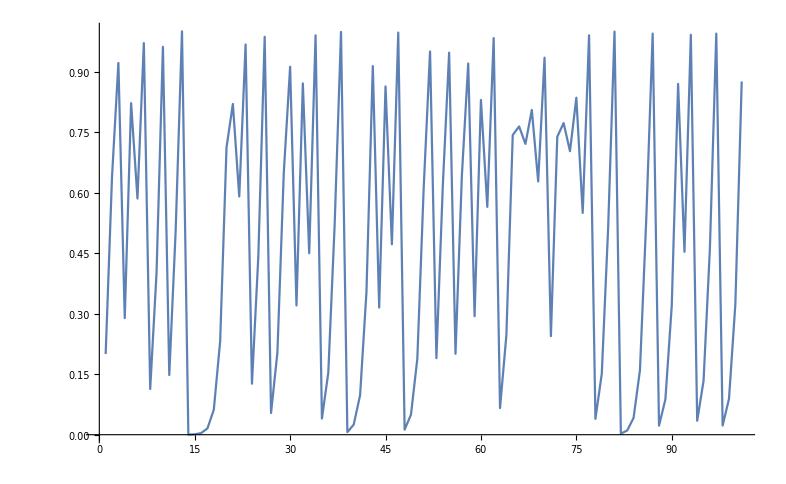

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]]
```

```mathematica
(*В самом начале графика мы видим значение 0.9, но это не вторая точка. Это третья точка. Из-за масштаба нам кажется, что отрезки от 1 до 2 и от 2 до 3 - единая линия. Это неверно. Чтобы увидеть значение для второй точки нужно приблизить график, например заменить 100 итераций на 10 *)
NestList[4 #(1-#)&,0.2,100]
```

{0.2,0.64,0.9216,0.289014,0.821939,0.585421,0.970813,0.113339,0.401974,0.961563,0.147837,0.503924,0.999938,0.000246305,0.000984976,0.00393603,0.0156821,0.0617448,0.23173,0.712124,0.820014,0.590364,0.967337,0.126384,0.441645,0.986379,0.053742,0.203415,0.64815,0.912207,0.320342,0.870893,0.449755,0.989902,0.0399856,0.153547,0.519882,0.998419,0.00631451,0.0250985,0.0978744,0.35318,0.913776,0.315159,0.863335,0.47195,0.996853,0.0125495,0.0495681,0.188445,0.611733,0.950063,0.189772,0.615035,0.947067,0.200523,0.641254,0.920189,0.293764,0.829868,0.56475,0.98323,0.0659554,0.246421,0.742791,0.76421,0.720773,0.805037,0.62781,0.934659,0.244287,0.738444,0.772578,0.702804,0.835482,0.549808,0.990077,0.0393,0.151022,0.512857,0.999339,0.00264312,0.0105445,0.0417334,0.159967,0.53751,0.994372,0.0223857,0.0875383,0.319501,0.869681,0.453344,0.991293,0.0345245,0.13333,0.462213,0.994289,0.0227147,0.088795,0.323642,0.875591}

```mathematica
5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&,начиная с 1
```

```mathematica
Nest[1+1/#&,1,30]
```

2178309/1346269

```mathematica
6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения.
```

```mathematica
Table[3^(i-1),{i,10}]
```

{1,3,9,27,81,243,729,2187,6561,19683}

```mathematica
7. Составьте список результатов действия вложенной функции (метод Ньютона) (#+2/#)/2 до
5 раз,начиная с 1.0,а затем вычтитекорень из 2 из всех результатов.
```

```mathematica
NestList[(#+2/#)/2 -Sqrt[2]&,1.0,5]
```

{1.,0.0857864,10.2855,3.82578,0.76006,0.281502}

```mathematica
8. Создайте список из 5 степеней числа 2,т.е.2^2^2...^2 n раз,причем n меняется от 0 до 4.
```

```mathematica
Table[2^Random[Integer,{0,4}],{i,5}]
```

{2,1,8,2,16}

# 1.5

```mathematica
1. Определите функцию f,которая вычисляет квадрат ее аргумента.
```

```mathematica
f[x_]:=x^2
f[9]
```

81

```mathematica
2. Определите функцию poly,которая имеет целочисленное значение аргумента и создает изображение оранжевого правильного многоугольника с числом сторон,равным значению этого аргумента.
```

```mathematica
(*Polygon[{P1,...,Pn}] представляет собой заполненный многоугольник с точками Pi
CirclePoints даёт угловые координаты для обычного многоугольника*)
```

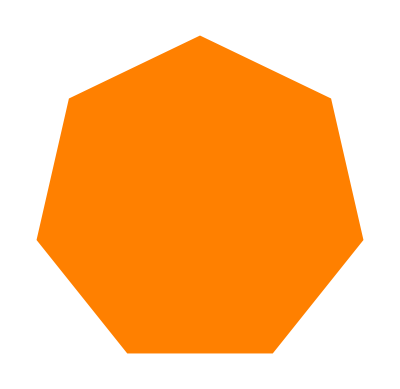

```mathematica
poly[x_]:=Graphics[{Orange,Polygon[CirclePoints[x]]}] 
poly[7]
```

```mathematica
3. Определите функцию f,которая берет список из двух элементов и помещает их в обратном
порядке.
```

```mathematica
f[{x1_, x2_}]:= {x2, x1}
f[{1,2}]
```

{2,1}

```mathematica
4.Определите функцию f,которая имеет два аргумента и дает результат в виде дроби,где
числитель равен произведению этих элементов,а знаменатель-их сумме.
```

```mathematica
f[x1_, x2_]:= x1*x2/(x1+x2)
f[2,4]
```

4/3

```mathematica
5. Определите функцию f,которая имеет два аргумента и дает результат в виде списка трех
элементов,которые соответственно равны сумме,разности и частному этих аргументов.
```

```mathematica
f[x1_, x2_]:= {x1+x2, x1-x2, x1/x2}
f[18,3]
```

{21,15,6}

```mathematica
6. Определите функцию evenodd,которая зависит от одного целочисленного аргумента и
имеет значение Black,если ее аргумент четный,значение-White в противном случае,значение
Red-если аргумент равен нулю
```

```mathematica
(*If[condition,t,f] возвращает t, если condition истинно, и f, если ложно
EvenQ[x] возвращает True, если x является чётным числом, и False в противном случае*)
```

```mathematica
evenodd[x_]:= If[x!=0,If[EvenQ[x],Black,White],Red]
evenodd[0]
```

RGBColor[1, 0, 0]

```mathematica
7. Определите функцию Fibonacci f с f[0]=1 и f[1]=1,а f[n] для натурального числа n является
суммой f[n-1] и f[n-2].
```

```mathematica
f[n_]:= f[n-1]+f[n-2]
f[1]:=1
f[2]:=1
f[6]
```

8